```mathematica
<< /home/pablo/Escritorio/Uni/RRT/drawTx.m
```

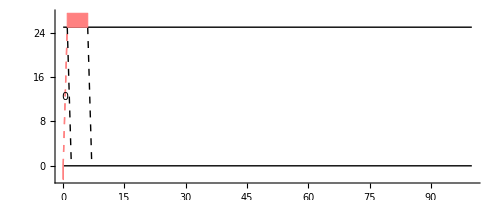

```mathematica
SetIniParDraw[1,5]
a={0,20,0,0,0};
Show[DrawWin[0,100,8],DrawPacketTx[a]]
```

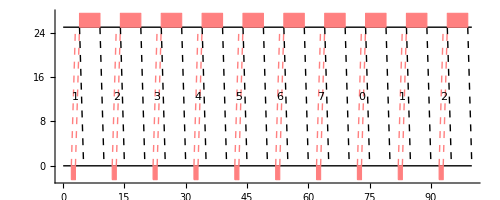

```mathematica
lstPck=Table[{2+n*10,9600,n+1,0,0},{n,0,9}];
Show[DrawWin[0,100,8],Map[DrawPacketTx[#]&,lstPck]]
```

```mathematica
SetIniParDraw[.5,0]
a={0,9600,0,0,0};
Show[DrawWin[0,100,8],DrawPacketTx[a]]
```